# Powtórka - liczby w pamięci komputera

## Liczby całkowite

### Liczby naturalne

Liczby zapisujemy w systemie pozycyjnym - zazwyczaj  jako potęgi liczby 10

```mathematica
3 * 10^2 + 9 * 10^1 + 2 * 10^0
```

W informatyce - stosuje się system dwójkowy

```mathematica
1 * 2^5 + 0 * 2^4 + 1 * 2^3 + 0 * 2^2 + 1 * 2^1 + 0 * 2^0
```

Zakres: 0 do 2^(liczba bitów)-1

```mathematica
BaseForm[153,2]
```

10011001_2

## Liczby całkowite

### Liczby ujemne

kod uzupełnień do dwóch:

```mathematica
0*(-2^6) + 1 * 2^5 + 0 * 2^4 + 1 * 2^3 + 0 * 2^2 + 1 * 2^1 + 0 * 2^0
```

42

przepis na “-42”: zamień wszystkie bity na przeciwne i dodaj 1

```mathematica
1*(-2^6) + 0 * 2^5 + 1 * 2^4 + 0 * 2^3 + 1 * 2^2 + 0 * 2^1 + 1 * 2^0 + 1
```

-42

jednoznaczne zero

## Liczby zmiennoprzecinkowe

W systemie dziesiętnym 454.574=

```mathematica
N[4 * 10^2 + 5 * 10^1 + 4 * 10^0 + 5 * 10^-1 + 7 * 10^-2 + 4 * 10^-3]
```

454.574

Ale też 1/3 =  0 * 10^0 + 3 * 10^-1 + 3 * 10^-2 + 3 * 10^-3 + ...

W systemie binarnym 12.625 =

```mathematica
N[1 * 2^3 + 1 * 2^2 + 0 * 2^1 + 0 * 2^0 + 1 * 2^-1 + 0 * 2^-2 + 1 * 2^-3  ]
```

```mathematica
BaseForm[13.625,2]
```

1101.101_2

Ale 0.1 =

```mathematica
BaseForm[0.1,2]
```

0.00011001100110011001101_2

```mathematica
N[0*2^-1+0*2^-2+0*2^-3+1*2^-4+1*2^-5+0*2^-6+0*2^-7+1*2^-8+1*2^-9+0*2^-10+0*2^-11+1*2^-12+1*2^-13+0*2^-14+0*2^-15+1*2^-16+1*2^-17+0*2^-18+0*2^-19+1*2^-20+1*2^-21+0*2^-22+1*2^-23,10]
```

## Liczby zmiennoprzecinkowe: IEEE 754

### Reprezentacja liczb: ±mantysa * 2^cecha

```mathematica
BaseForm[145.1135,2]
```

1.0010001000111010001_2×2^7

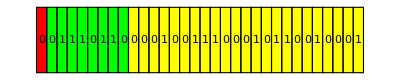

```mathematica
rand=RandomChoice[{0,1},32];
Graphics[Table[{EdgeForm[Black],If[i==0,FaceForm[Red],If[i>0&&i<9,FaceForm[Green],FaceForm[Yellow]]],Rectangle[{i,0},{i+1,1}],Black,Text[ToString[rand[[i+1]]],{i+0.5,0.5}]},{i,0,31}],ImageSize->Full]
```

```mathematica
If[rand[[1]]==1,sign =-1,sign =1]
wykladnik = Total[Table[rand[[2+i]]*2^(7-i),{i,0,7}]]-127
mantysa = 1+N@Total[Table[rand[[10+i]]*2^(-i-1),{i,0,22}]]
N[sign*mantysa * 2^wykladnik]
```

1

-9

1.07634

0.00210223

Przypadki specjalne

0^+

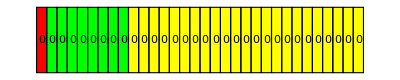

```mathematica
Graphics[Table[{EdgeForm[Black],If[i==0,FaceForm[Red],If[i>0&&i<9,FaceForm[Green],FaceForm[Yellow]]],Rectangle[{i,0},{i+1,1}],Black,Text[ToString[0],{i+0.5,0.5}]},{i,0,31}],ImageSize->Full]
```

0^-

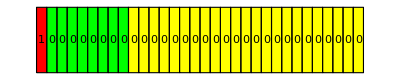

```mathematica
Graphics[Table[{EdgeForm[Black],If[i==0,FaceForm[Red],If[i>0&&i<9,FaceForm[Green],FaceForm[Yellow]]],Rectangle[{i,0},{i+1,1}],Black,Text[ToString[If[i==0,1,0]],{i+0.5,0.5}]},{i,0,31}],ImageSize->Full]
```

±∞  (mantysa = same zera)

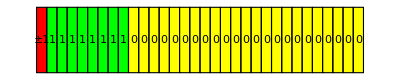

```mathematica
Graphics[Table[{EdgeForm[Black],If[i==0,FaceForm[Red],If[i>0&&i<9,FaceForm[Green],FaceForm[Yellow]]],Rectangle[{i,0},{i+1,1}],Black,Text[ToString[If[i==0,HoldForm[±1],If[i<9,1,0]]],{i+0.5,0.5}]},{i,0,31}],ImageSize->Full]
```

NaN (mantysa może być niezerowa)

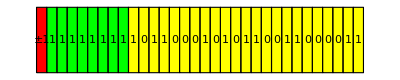

```mathematica
Graphics[Table[{EdgeForm[Black],If[i==0,FaceForm[Red],If[i>0&&i<9,FaceForm[Green],FaceForm[Yellow]]],Rectangle[{i,0},{i+1,1}],Black,Text[ToString[If[i==0,HoldForm[±1],If[i<9,1,RandomChoice[{0,1},1][[1]]]]],{i+0.5,0.5}]},{i,0,31}],ImageSize->Full]
```

## Liczba maszynowa vs liczba rzeczywista

```mathematica
N[2^-24]
```

5.96046×10^-8

## Błąd względny i bezwzględny

Błąd bezwzględny:|x-x_p|  (x_p: przybliżenie liczby x)
Błąd względny: (|x-x_p|)/x

### Przykład: wzór Stirlinga: n! ≈ (n/e)^n √(2π n)

```mathematica
stir[n_]:=√(2π n)(n/E)^n
```

```mathematica
m = 100
N[m!]
N[stir[m]]
 Abs[N[m!]-N[stir[m]]]/N[m!]*100   (*błąd względny*)
Abs[N[m!]-N[stir[m]]]    (*błąd bezwzględny*)
```

100

9.33262×10^157

9.32485×10^157

0.0832983

7.77392×10^154

## Utrata liczb znaczących

Należy być też ostrożnym przy odejmowaniu bliskich sobie wartości.

### √(x^2+1)-1 vs x^2/(√(x^2+1)+1)

```mathematica
(*Mathematica jest na tyle inteligentna, że sobie poradzi z takim problemem*)
```

Kod źródłowy w C++

#include < iostream > 
#include < cmath > 

float f1 (float x) {
	return std::sqrtf (x*x + 1) - 1;
	}

float f2 (float x) {
	return x*x/(std::sqrtf (x*x + 1) + 1);
	}

int main () {
	float val {}, step = 0.00001;
  	for (int i = 0; i < 100; i++) {
  		val = step*i;
    	std::cout << " x = " << val << "; " << f1 (val) << " " << f2 (val) << std::endl;
    	}
    return 0;	
	}

Możemy też skorzystać z szeregu Taylora: f(x)=∑_(k=1)^n 1/(k!)f^(k)(c)(x-c)^k+1/((n+1)!)f^(n+1)(ξ)(x-c)^(n+1).

### Obliczyć wartość wyrażenia Log[x+1]-x dla x bliskich zera .

```mathematica
Normal[Series[Log[x+1]-x,{x,0,5}]]
```

-x^2/2+x^3/3-x^4/4+x^5/5

```mathematica
Table[{N@x,N[Log[x+1]-x]},{x,10^-5,0.00029,10^-5}]
```

{{0.00001,-4.99996×10^-11},{0.00002,-1.99997×10^-10},{0.00003,-4.49991×10^-10},{0.00004,-7.99979×10^-10},{0.00005,-1.24996×10^-9},{0.00006,-1.79993×10^-9},{0.00007,-2.44989×10^-9},{0.00008,-3.19983×10^-9},{0.00009,-4.04976×10^-9},{0.0001,-4.99967×10^-9},{0.00011,-6.04956×10^-9},{0.00012,-7.19942×10^-9},{0.00013,-8.44927×10^-9},{0.00014,-9.79909×10^-9},{0.00015,-1.12489×10^-8},{0.00016,-1.27986×10^-8},{0.00017,-1.44484×10^-8},{0.00018,-1.61981×10^-8},{0.00019,-1.80477×10^-8},{0.0002,-1.99973×10^-8},{0.00021,-2.20469×10^-8},{0.00022,-2.41965×10^-8},{0.00023,-2.64459×10^-8},{0.00024,-2.87954×10^-8},{0.00025,-3.12448×10^-8},{0.00026,-3.37941×10^-8},{0.00027,-3.64434×10^-8},{0.00028,-3.91927×10^-8},{0.00029,-4.20419×10^-8}}

```mathematica
(*Mathematica znowu sobie radzi*)
```

### Oblicz wartość funkcji sinus dla argumentu typu float (4 bajty) x = 24684.1516

Mathematica daje wynik:

```mathematica
N[Sin[24684.1516]]
```

-0.611631

W C++ funkcja: std::sin(24684.1516f) daje -0.612219

Rozwiązania problemu:

użyć zmiennej o większej dokładności (double’a): std::sin(24684.1516) = -0.611631

Wykorzystać periodyczność funkcji sinus: 24684.1516=3928*2π +3.7997  =>std::sin(3.7997f) = -0.611621

```mathematica
Mod[24684.1516,2π]
```

3.79971

## Znaj swoje szeregi

### Spróbujmy obliczyć liczbę π z dokładnością do piątego miejsca po przecinku

#### Sposób naiwny: π^2/6=∑_(k=1)^∞ 1/k^2 więc π=√(6∑_(k=1)^∞ 1/k^2)

```mathematica
AbsoluteTiming@N[√(6*Sum[1/i^2,{i,1,100000}]),10]
N[π,10]
Abs[N[π,10]-N[√(6*Sum[1/i^2,{i,1,100000}]),10]]
```

{3.92185,3.141583104}

3.141592654

9.549×10^-6

#### Sposób lepszy: 1/π = (2 √2)/99^2∑_(k=0)^∞ ((4k)!)/(k!)^4(26390k+1103)/396^(4k)

```mathematica
N[π,40]
AbsoluteTiming@N[1/Sum[(2 √2)/99^2((4k)!)/(k!)^4*(26390k+1103)/396^(4k),{k,0,10}],40]
Abs[N[π,40]-N[1/Sum[(2 √2)/99^2((4k)!)/(k!)^4*(26390k+1103)/396^(4k),{k,0,3}],40]]
```

3.141592653589793238462643383279502884197

{0.0007701,3.141592653589793238462643383279502884197}

5.238896×10^-32

#### Inny szereg: π=∑_(k=0)^∞ (-1)^k/4^k(2/(4k+1)+2/(4k+2)+1/(4k+3))

```mathematica
AbsoluteTiming[N[Sum[(-1)^k/4^k(2/(4k+1)+2/(4k+2)+1/(4k+3)),{k,0,10}],10]]
Abs[N[π,10]-N[Sum[(-1)^k/4^k(2/(4k+1)+2/(4k+2)+1/(4k+3)),{k,0,10}],10]]
```

{0.0001779,3.141592675}

2.×10^-8

2.×10^-8

## Ciekawostka - mnożenie macierzy

Mnożenie jest “droższe” od dodawania

```mathematica
A=({{a1, a2}, {a3, a4}})
B=({{b1, b2}, {b3, b4}})
A.B
```

{{a1,a2},{a3,a4}}

{{b1,b2},{b3,b4}}

{{a1 b1+a2 b3,a1 b2+a2 b4},{a3 b1+a4 b3,a3 b2+a4 b4}}

### Algorytm Strassena

Dla macierzy 4x4 algorytm Strassena potrzebuje 49 mnożeń.
AlphaTensor znalazł(?a) sposób z 47 mnożeniami

# Interpolacja i ekstrapolacja

## Interpolacja - znajdowanie nowych wartości dla znanego zbioru danych

```mathematica
Show[{ListPlot[Table[i^2,{i,1,10}]],Graphics[{PointSize[0.01],Red,Point[{5.5,5.5^2}]}]},LabelStyle->{13,GrayLevel[0]}]
```

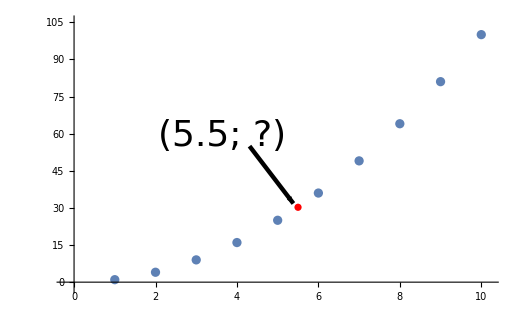

## Ekstrapolacja - znajdowanie nowych wartości dla znanego zbioru danych, ale poza zakresem danych

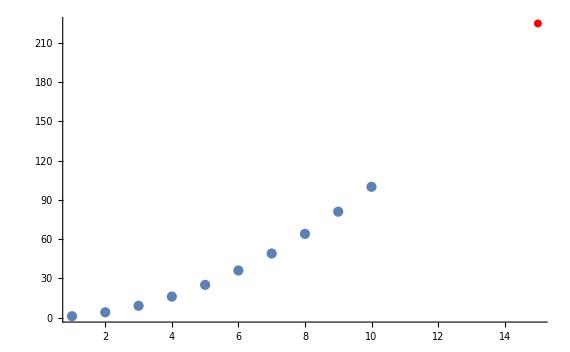

```mathematica
Show[{ListPlot[Table[i^2,{i,1,10}]],Graphics[{PointSize[0.01],Red,Point[{15,15^2}]}]},LabelStyle->{13,GrayLevel[0]},PlotRange->All]
```

## Interpolacja stała - wartość pomiędzy punktami jest taka sama jak najbliższego elementu

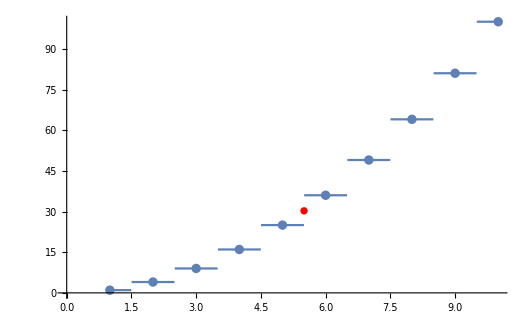

```mathematica
Show[{ListPlot[Table[i^2,{i,1,10}]],Plot[Ceiling[x-.5]^2,{x,1,10}],Graphics[{PointSize[0.01],Red,Point[{5.5,5.5^2}]}]},LabelStyle->{13,GrayLevel[0]}]
```

## Interpolacja liniowa - przybliżamy wartość funkcji między dwoma punktami funkcją liniową

InterpolatingFunction[…]

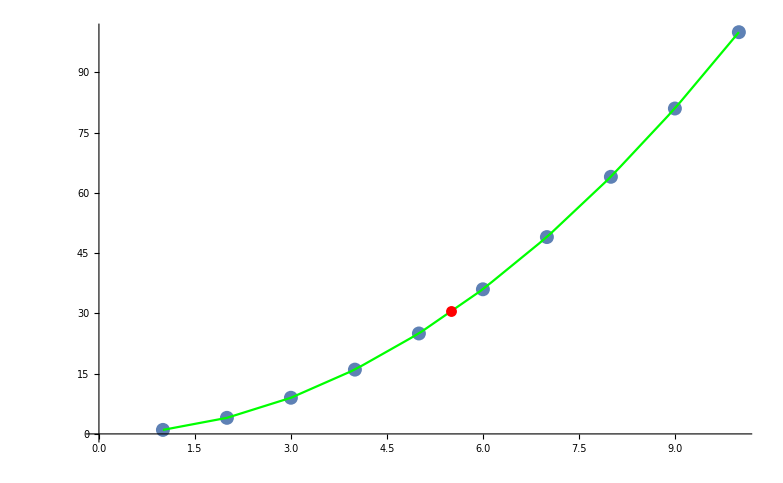

```mathematica
inter=Interpolation[Table[{i,i^2},{i,1,10}],InterpolationOrder->1]
Show[{ListPlot[Table[i^2,{i,1,10}]],Plot[inter[x],{x,1,10},PlotStyle->Green],Graphics[{PointSize[0.01],Red,Point[{5.5,inter[5.5]}]}]},LabelStyle->{13,GrayLevel[0]}]
```

### Znajdźmy wartość funkcji dla x = 5.5

Znamy wartości funkcji f dla f(5) = 25 oraz f(6) = 36. Znajdujemy prostą przechodzącą przez oba punkty:

```mathematica
line=SolveValues[ { 25 == a * 5 + b, 36 == a * 6 + b   },{a,b}][[1]]
```

{11,-30}

Więc nasza interpolacja dla x∈ [a,b] to y = 11 x - 30. Dla x = 5.5, y =  30.5 (prawdziwa wartość to 30.25).

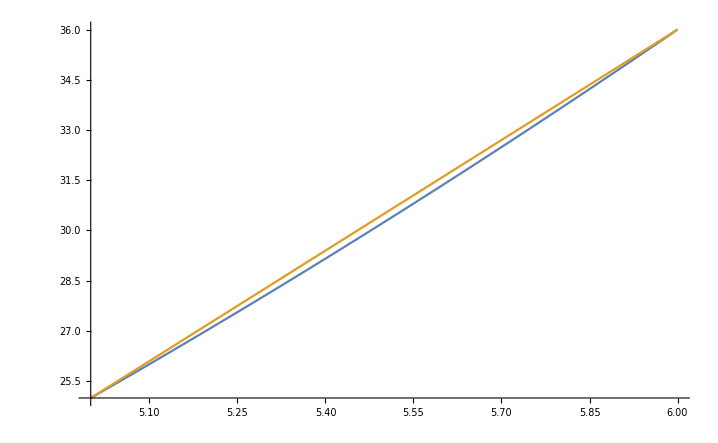

```mathematica
Plot[{x^2, 11x-30},{x,5,6}]
```

## Interpolacja wielomianowa

Dla  n + 1 punktów (o różnych współrzędnych x-owych) istnieje tylko jeden wielomian stopnia n, który przechodzi przez wszystkie punkty

### Interpolacja Lagrange’a

Wielomianem Lagrange’a nazywamy wielomian L(x) = ∑_(j=0)^k y_j*l_j(x), gdzie 
l_j(x)=∏_(0<= m<= k
m!= j) (x - x_m)/(x_j - x_m)

#### Przykład: znajdź wielomian Lagrange’a dla podanych 4 punktów:

```mathematica
{x0,y0} = {0,2};
{x1,y1} = {0.5,1.125};
{x2,y2} = {1.5,-0.625};
{x3,y3} = {3,8};
```

```mathematica
l0  = (x - x1)/(x0 - x1)(x - x2)/(x0 - x2)(x - x3)/(x0 - x3)
l1  = (x - x0)/(x1- x0)(x - x2)/(x1 - x2)(x - x3)/(x1 - x3)
l2  =(x - x0)/(x2 - x0) (x - x1)/(x2 - x1)(x - x3)/(x2 - x3)
l3  = (x - x0)/(x3 - x0)(x - x1)/(x3 - x1)(x - x2)/(x3 - x2)
L = y0 * l0 + y1*l1 + y2 * l2+y3*l3
Simplify[L]
```

0.444444 (3-x) (-1.5+x) (-0.5+x)

0.8 (-3+x) (-1.5+x) x

-0.444444 (-3+x) (-0.5+x) x

0.0888889 (-1.5+x) (-0.5+x) x

0.888889 (3-x) (-1.5+x) (-0.5+x)+0.9 (-3+x) (-1.5+x) x+0.277778 (-3+x) (-0.5+x) x+0.711111 (-1.5+x) (-0.5+x) x

2.-1. x-2. x^2+1. x^3

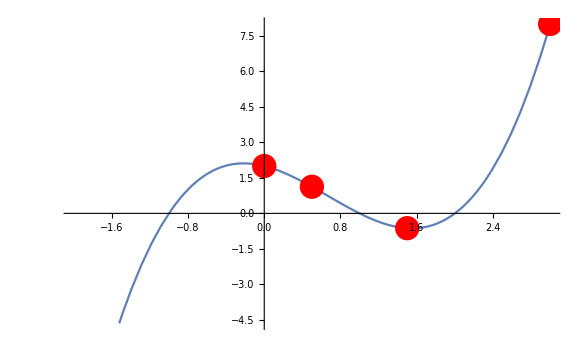

```mathematica
Show[{Plot[{L},{x,-2,3}],Graphics[{Red,PointSize[0.03],Point[{{x1,y1},{x2,y2},{x3,y3},{x0,y0}}]}]}]
```

0.444444 (3-x) (-1.5+x) (-0.5+x)

0.8 (-3+x) (-1.5+x) x

-0.444444 (-3+x) (-0.5+x) x

0.0888889 (-1.5+x) (-0.5+x) x

0.888889 (3-x) (-1.5+x) (-0.5+x)+0.9 (-3+x) (-1.5+x) x+0.277778 (-3+x) (-0.5+x) x+0.711111 (-1.5+x) (-0.5+x) x

2.-1. x-2. x^2+1. x^3

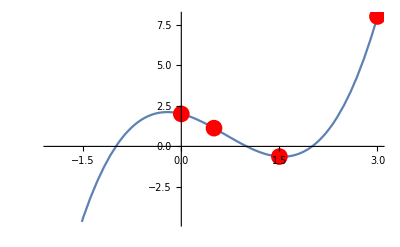

```mathematica
l1= (x-x2)/(x1-x2)*(x-x3)/(x1-x3)*(x-x4)/(x1-x4)
l2= (x-x1)/(x2-x1)*(x-x3)/(x2-x3)*(x-x4)/(x2-x4)
l3= (x-x1)/(x3-x1)*(x-x2)/(x3-x2)*(x-x4)/(x3-x4)
l4= (x-x1)/(x4-x1)*(x-x2)/(x4-x2)*(x-x3)/(x4-x3)
L=l1 * y1+l2 * y2+l3 * y3+l4 * y4
Expand@FullSimplify[L]
Show[{Plot[{L},{x,-2,3}],Graphics[{Red,PointSize[0.03],Point[{{x1,y1},{x2,y2},{x3,y3},{x4,y4}}]}]}]
```

## Algorytm Neville’a

Alternatywny sposób obliczania wielomianu Lagrange’a:
p_ii= y_i
p_ij=((x - x_i)p_(i+1 j) - (x-x_j) p_(i j-1))/(x_j-x_i)
poszukujemy p_(0n)

```mathematica
Grid[{{"p00","p01","p02","p03","p04"},{"","p11","p12","p13","p14"},{"","","p22","p23","p24"},{"","","","p33","p34"},{"","","","","p44"}},Frame->All,Spacings->{2,2}]
```

p00 | p01 | p02 | p03 | p04
 | p11 | p12 | p13 | p14
 |  | p22 | p23 | p24
 |  |  | p33 | p34
 |  |  |  | p44

```mathematica
{x0,y0} = {0,2};
 {x1,y1} = {0.5,1.125};
{x2,y2}= {1.5,-0.625};
{x3,y3}  = {3,8};
```

```mathematica
p00 = y0
p11 = y1
p22 = y2
p33 = y3
p01 = ((x-x0)p11-(x-x1)p00)/(x1-x0)
p12 = ((x-x1)p22-(x-x2)p11)/(x2-x1)
p02 = ((x-x0)p12-(x-x2)p01)/(x2-x0)
p23 = ((x-x2)p33-(x-x3)p22)/(x3-x2)

p13 = ((x-x1)p23-(x-x3)p12)/(x3-x1)

p03 = ((x-x0)p13-(x-x3)p02)/(x3-x0)
```

2

1.125

-0.625

8

2. (-2 (-0.5+x)+1.125 x)

1. (-1.125 (-1.5+x)-0.625 (-0.5+x))

0.666667 (1. (-1.125 (-1.5+x)-0.625 (-0.5+x)) x-2. (-1.5+x) (-2 (-0.5+x)+1.125 x))

0.666667 (0.625 (-3+x)+8 (-1.5+x))

0.4 (-1. (-1.125 (-1.5+x)-0.625 (-0.5+x)) (-3+x)+0.666667 (0.625 (-3+x)+8 (-1.5+x)) (-0.5+x))

1/3 (0.4 (-1. (-1.125 (-1.5+x)-0.625 (-0.5+x)) (-3+x)+0.666667 (0.625 (-3+x)+8 (-1.5+x)) (-0.5+x)) x-0.666667 (-3+x) (1. (-1.125 (-1.5+x)-0.625 (-0.5+x)) x-2. (-1.5+x) (-2 (-0.5+x)+1.125 x)))

```mathematica
Simplify[p03]
```

2.-1. x-2. x^2+1. x^3